## Backreaction of massless scalar to de Sitter spacetime

This is a supplementary Mathematica notebook to the paper “Inflationary quantum dynamics and backreaction using a classical-quantum correspondence”. We use the CQC (classical-quantum correspondence) to study the quantum dynamics, including the back-reaction, of a massless scalar field in a cosmological background.

Author: Reggie Bernardo

### I. de Sitter spacetime

We shall work with conformal time t in which the scale factor a(t) for a de Sitter universe is given by...

```mathematica
ads=a->Function[t,A/(1-A H t)];
"a(t)"==a[t]/.ads
```

a(t)==A/(1-A H t)

This can be obtained as a semiclassical approximation to the coupled Einstein-scalar system. In this case, we consider the Friedmann equations

```mathematica
FE1=3 a'[t]^2/a[t]^4==ρΛ;
FE2=2 a''[t]/a[t]^3-a'[t]^2/a[t]^4==-PΛ;

FE1
FE2
```

(3 a'[t]^2)/a[t]^4==ρΛ

-a'[t]^2/a[t]^4+(2 a''[t])/a[t]^3==-PΛ

It is easy to see that the Friedmann equations are satisfied by ads together with ρ_Λ=3 H^2 and P_Λ=-ρ_Λ...

```mathematica
FE1/.ρΛ->3 H^2/.ads//Simplify
FE2/.PΛ->-ρΛ/.ρΛ->3 H^2/.ads//Simplify
```

True

True

For what follows we are also interested in obtaining this solution numerically. To do so using a second-order differential equation, we eliminate a'(t) dependence in FE2 using FE1...

(2 a''[t])/a[t]^3==4 H^2

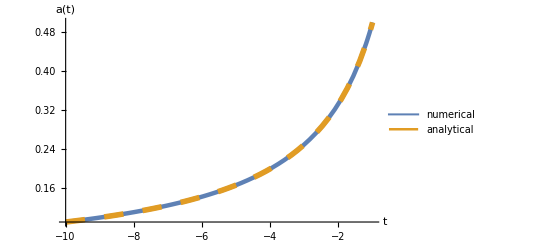

```mathematica
(*initial conditions at any t can be obtained using ads*)

FE12=(FE2/.Solve[FE1,a'[t]][[2]]/.PΛ->-ρΛ/.ρΛ->3 H^2//Simplify);FE12

param={ti->-10,tf->-1,A->1,H->1};
solFE12=NDSolve[{FE12,a[ti]==A/(1-A H ti),a'[ti]==(A^2 H)/(1-A H ti)^2}/.param,a,{t,ti,tf}/.param][[1]];
Plot[{a[t]/.solFE12,a[t]/.ads/.param},{t,ti,tf}/.param,PlotRange->All,AxesLabel->{"t","a(t)"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"numerical","analytical"},PlotStyle->{Thickness[0.008],{Dashing[Large],Thickness[0.01]}}]
```

### II. CQC

The CQC version of the Friedmann equations are given by...

```mathematica
ρϕvac=ρϕ->Function[t,1/(2 a[t]^4)((ξ'[t]^2+(k^2+a'[t]^2/a[t]^2)ξ[t]^2-2 a'[t]/a[t] ξ[t]ξ'[t])+(χ'[t]^2+(k^2+a'[t]^2/a[t]^2)χ[t]^2-2 a'[t]/a[t] χ[t]χ'[t]))];

fe1=3 a'[t]^2/a[t]^4==ρΛ+ρϕ[t];
fe2=2 a''[t]/a[t]^3-a'[t]^2/a[t]^4==-PΛ-ρϕ[t];
```

We eliminate the a'(t)^2/(a(t))^4 term in fe2 using fe1...

```mathematica
fe12=(fe2/.Solve[fe1,a'[t]][[2]]//Simplify);fe12
```

PΛ+ρϕ[t]+(2 a''[t])/a[t]^3==1/3 (ρΛ+ρϕ[t])

This is the ODE that we intend to solve with the CHOs ξ(t) and χ(t) using the CQC. To compare the results with just de Sitter inflation, a(t)=A/(1-A H t), we use the same initial conditions for the scale factor...

```mathematica
ainit={a[ti]->A/(1-A H ti),a'[ti]->(A^2 H)/(1-A H ti)^2};
ρϕ0=ρϕ[ti]->ω/(4 a[ti]^4)(1+((k^2+(a'[ti]/a[ti])^2)/ω^2))/.ainit//Simplify;
```

Consequently, this means that the cosmological constant’s energy density is not equal to 3 H^2 but is instead...

```mathematica
ρΛ0=Solve[fe1/.t->ti/.ρϕ0/.ainit,ρΛ][[1]];

"ρΛ"==ρΛ/.ρΛ0
```

ρΛ==3 H^2-((-1+A H ti)^4 (1+(k^2+(A^2 H^2)/(-1+A H ti)^2)/ω^2) ω)/(4 A^4)

Finally, the CQC equations are given by...

```mathematica
cqc={(fe12/.PΛ->-ρΛ/.ρΛ0/.ρϕvac//Simplify),ξ''[t]+(k^2-a''[t]/a[t])ξ[t]==0,χ''[t]+(k^2-a''[t]/a[t])χ[t]==0,a[ti]==(a[ti]/.ainit[[1]]),a'[ti]==(a'[ti]/.ainit[[2]]),ξ[ti]==0,ξ'[ti]==√(ω/2),χ[ti]==-1/(√(2ω)),χ'[ti]==0};
```

To perform the integration we specify the constants k (mode’s wave number), σ (width of wave packet in ψ_k configuration space), A, H, and ω (initial frequency). These constants are, however, not independent of each other and in fact we can arbitrarily specify only 4 of them. We take ω to depend on the other constants. Recall that...

```mathematica
ωdef=Solve[ω^2==k^2-1/2(a'[t]^2/a[t]^2+a[t]^2(ρΛ-ρϕ[t]))/.t->ti/.ρϕ0/.ainit/.ρΛ0,ω][[1]]//Simplify;
```

It is convenient at this point to show the plots of the initial values of ρ_ϕ(k) and ρ_Λ(k) (or rather their density parameters, i.e., Ω_i=ρ_i/(3 H^2)) in anticipation of the result that long wavelength-modes (k≪1) backreact more strongly compared to some short wavelength-modes...

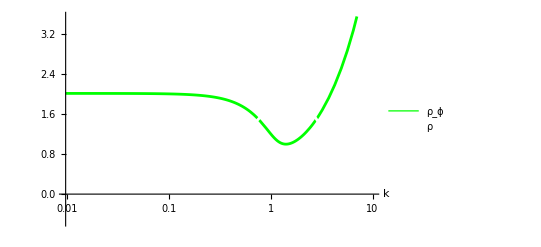

```mathematica
LogLinearPlot[{ρϕ[ti]/.ρϕ0/.ωdef/.ti->0/.{A->1,H->1},ρΛ/.ρΛ0/.ωdef/.ti->0/.{A->1,H->1}},{k,0,10},AxesLabel->{"k",""},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"ρ_ϕ","ρ"},PlotStyle->{{Thickness[0.005],Green},{Dashing[Large],Thickness[0.005],White}}]
```

At last, we numerically integrate the dynamical system using the following function...

```mathematica
cqcint[A0_,H0_,k0_,ti0_,tf0_]:=(
param={ti->ti0,tf->tf0,A->A0,H->H0,k->k0};
nsol=NDSolve[cqc/.ωdef/.param,{a,ξ,χ},{t,ti,tf}/.param,WorkingPrecision->30][[1]];
Hvac[t_]=ξ'[t]^2/2+(k^2-a''[t]/a[t])ξ[t]^2+χ'[t]^2/2+(k^2-a''[t]/a[t])χ[t]^2/.param/.nsol;
ωsq[t_]=k^2-a''[t]/a[t]/.param/.nsol;
βsq[t_]=Hvac[t]/(√ωsq[t])-1/2;
{(ω/.ωdef/.param//N),(ρϕ[ti]/.ρϕ0/.ωdef/.param//N),(ρΛ/.ρΛ0/.ωdef/.param//N),nsol,Hvac[t],ωsq[t],βsq[t],ρϕ[t]/.ρϕvac/.ωdef/.param/.nsol}
);
(*
Outputs: 4 = (a,ξ,χ), 5 = <0|H|0>(t), 6 = ω^2(t), 7 = |β|^2, 8 = <0|Subscript[ρ, ϕ](t)|0>
*)
```

We probe the k-dependence of the results first...

We plot test solutions below...

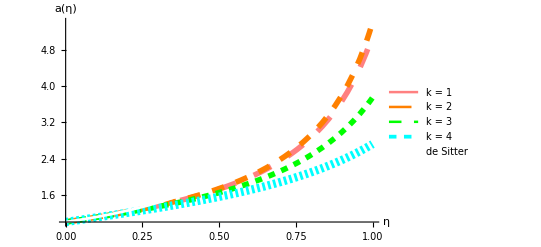

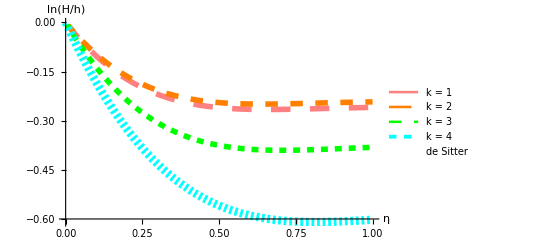

```mathematica
test1=cqcint[1,1,1,0,1];
test2=cqcint[1,1,2,0,1];
test3=cqcint[1,1,3,0,1];
test4=cqcint[1,1,4,0,1];
(*cutoff is 5.78*)

Plot[{a[t]/.test1[[4]],a[t]/.test2[[4]],a[t]/.test3[[4]],a[t]/.test4[[4]],a[t]/.ads/.param},{t,ti,tf}/.param,PlotRange->Automatic,AxesLabel->{"η","a(η)"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"k = 1","k = 2","k = 3","k = 4","de Sitter"},PlotStyle->{{Dashing[Large],Thickness[0.01],Pink},{Dashing[Medium],Thickness[0.01],Orange},{Dashing[Small],Thickness[0.01],Green},{Dashing[Tiny],Thickness[0.015],Cyan},{Thickness[0.005],White}}]

Plot[{Log[a'[t]/a[t]^2]/.test1[[4]],Log[a'[t]/a[t]^2]/.test2[[4]],Log[a'[t]/a[t]^2]/.test3[[4]],Log[a'[t]/a[t]^2]/.test4[[4]],Log[a'[t]/a[t]^2]/.ads/.param},{t,ti,tf}/.param,PlotRange->Automatic,AxesLabel->{"η","ln(H/h)"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"k = 1","k = 2","k = 3","k = 4","de Sitter"},PlotStyle->{{Dashing[Large],Thickness[0.01],Pink},{Dashing[Medium],Thickness[0.01],Orange},{Dashing[Small],Thickness[0.01],Green},{Dashing[Tiny],Thickness[0.015],Cyan},{Thickness[0.005],White}},AxesOrigin->{0,-0.6}]
```

The mode k=1 clearly backreacts more strongly than k=2 as anticipated.

We can also checkout the mode’s Hamiltonian, frequency, particle number, and energy density...

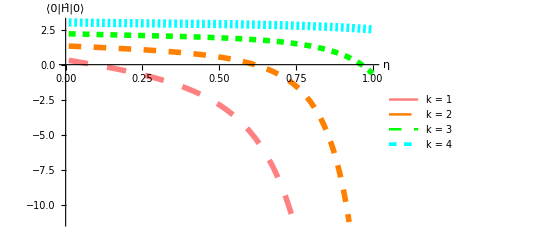

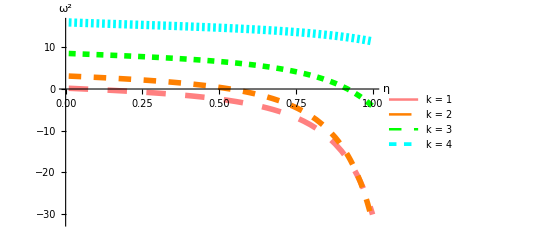

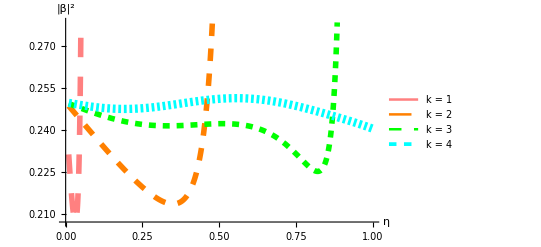

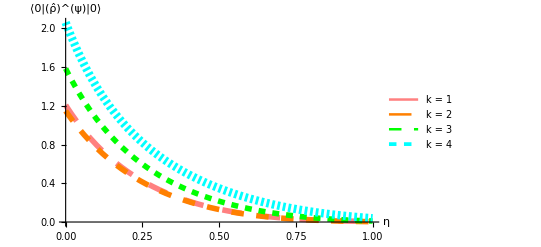

```mathematica
Plot[{test1[[5]],test2[[5]],test3[[5]],test4[[5]]},{t,ti+10^-2,tf}/.param,PlotRange->Automatic,AxesLabel->{"η","⟨0|Ĥ|0⟩"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"k = 1","k = 2","k = 3","k = 4"},PlotStyle->{{Dashing[Large],Thickness[0.01],Pink},{Dashing[Medium],Thickness[0.01],Orange},{Dashing[Small],Thickness[0.01],Green},{Dashing[Tiny],Thickness[0.015],Cyan}}]

Plot[{test1[[6]],test2[[6]],test3[[6]],test4[[6]]},{t,ti+10^-2,tf}/.param,PlotRange->Automatic,AxesLabel->{"η","ω^2"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"k = 1","k = 2","k = 3","k = 4"},PlotStyle->{{Dashing[Large],Thickness[0.01],Pink},{Dashing[Medium],Thickness[0.01],Orange},{Dashing[Small],Thickness[0.01],Green},{Dashing[Tiny],Thickness[0.015],Cyan}}]

Plot[{test1[[7]],test2[[7]],test3[[7]],test4[[7]]},{t,ti+10^-2,tf}/.param,PlotRange->Automatic,AxesLabel->{"η","|β|^2"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"k = 1", "k = 2","k = 3","k = 4"},PlotStyle->{{Dashing[Large],Thickness[0.01],Pink},{Dashing[Medium],Thickness[0.01],Orange},{Dashing[Small],Thickness[0.01],Green},{Dashing[Tiny],Thickness[0.015],Cyan}}]

Plot[{test1[[8]],test2[[8]],test3[[8]],test4[[8]]},{t,ti,tf}/.param,PlotRange->Automatic,AxesLabel->{"η","⟨0|(ρ̂)^(ψ)|0⟩"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"k = 1","k = 2","k = 3","k = 4"},PlotStyle->{{Dashing[Large],Thickness[0.01],Pink},{Dashing[Medium],Thickness[0.01],Orange},{Dashing[Small],Thickness[0.01],Green},{Dashing[Tiny],Thickness[0.015],Cyan}}]
```

There exists a cutoff above which the spacetime no longer continues to be de Sitter, i.e., destabilizes inflation.

Here is the cutoff plot...

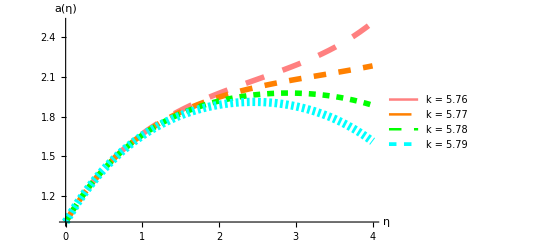

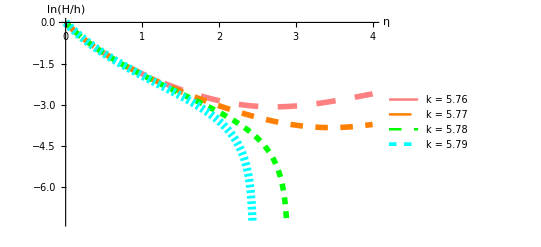

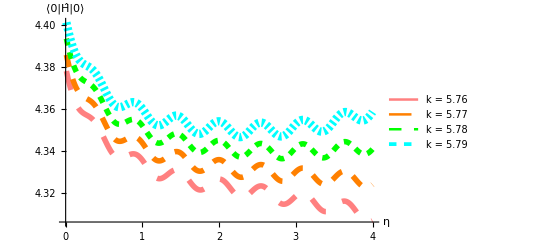

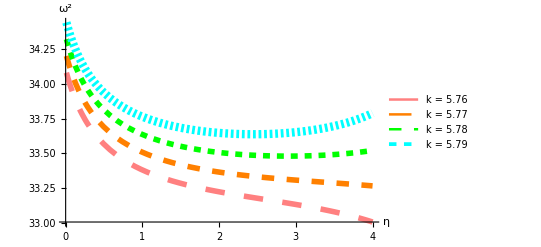

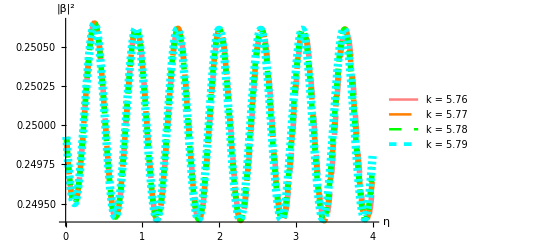

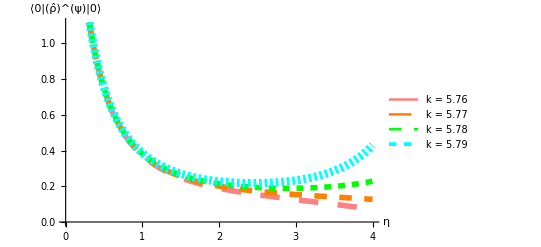

```mathematica
sck1=cqcint[1,1,5.76`100,0,4];
sck2=cqcint[1,1,5.77`100,0,4];
sck3=cqcint[1,1,5.78`100,0,4];
sck4=cqcint[1,1,5.79`100,0,4];
(*cutoff is 5.78*)

Plot[{a[t]/.sck1[[4]],a[t]/.sck2[[4]],a[t]/.sck3[[4]],a[t]/.sck4[[4]](*,a[t]/.ads/.param*)},{t,ti,tf}/.param,PlotRange->Automatic,AxesLabel->{"η","a(η)"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"k = 5.76","k = 5.77","k = 5.78","k = 5.79"(*,"de Sitter"*)},PlotStyle->{{Dashing[Large],Thickness[0.01],Pink},{Dashing[Medium],Thickness[0.01],Orange},{Dashing[Small],Thickness[0.01],Green},{Dashing[Tiny],Thickness[0.015],Cyan}(*,{Thickness[0.005],White}*)}]

Plot[{Log[a'[t]/a[t]^2]/.sck1[[4]],Log[a'[t]/a[t]^2]/.sck2[[4]],Log[a'[t]/a[t]^2]/.sck3[[4]],Log[a'[t]/a[t]^2]/.sck4[[4]](*,Log[a'[t]/a[t]^2]/.ads/.param*)},{t,ti,tf}/.param,PlotRange->Automatic,AxesLabel->{"η","ln(H/h)"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"k = 5.76","k = 5.77","k = 5.78","k = 5.79"},PlotStyle->{{Dashing[Large],Thickness[0.01],Pink},{Dashing[Medium],Thickness[0.01],Orange},{Dashing[Small],Thickness[0.01],Green},{Dashing[Tiny],Thickness[0.015],Cyan}(*,{Thickness[0.005],White}*)}]

Plot[{sck1[[5]],sck2[[5]],sck3[[5]],sck4[[5]]},{t,ti+10^-2,tf}/.param,PlotRange->Automatic,AxesLabel->{"η","⟨0|Ĥ|0⟩"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"k = 5.76","k = 5.77","k = 5.78","k = 5.79"},PlotStyle->{{Dashing[Large],Thickness[0.01],Pink},{Dashing[Medium],Thickness[0.01],Orange},{Dashing[Small],Thickness[0.01],Green},{Dashing[Tiny],Thickness[0.015],Cyan}}]

Plot[{sck1[[6]],sck2[[6]],sck3[[6]],sck4[[6]]},{t,ti+10^-2,tf}/.param,PlotRange->Automatic,AxesLabel->{"η","ω^2"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"k = 5.76","k = 5.77","k = 5.78","k = 5.79"},PlotStyle->{{Dashing[Large],Thickness[0.01],Pink},{Dashing[Medium],Thickness[0.01],Orange},{Dashing[Small],Thickness[0.01],Green},{Dashing[Tiny],Thickness[0.015],Cyan}}]

Plot[{sck1[[7]],sck2[[7]],sck3[[7]],sck4[[7]]},{t,ti+10^-2,tf}/.param,PlotRange->Automatic,AxesLabel->{"η","|β|^2"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"k = 5.76","k = 5.77","k = 5.78","k = 5.79"},PlotStyle->{{Dashing[Large],Thickness[0.01],Pink},{Dashing[Medium],Thickness[0.01],Orange},{Dashing[Small],Thickness[0.01],Green},{Dashing[Tiny],Thickness[0.015],Cyan}}]

Plot[{sck1[[8]],sck2[[8]],sck3[[8]],sck4[[8]]},{t,ti,tf}/.param,PlotRange->Automatic,AxesLabel->{"η","⟨0|(ρ̂)^(ψ)|0⟩"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"k = 5.76","k = 5.77","k = 5.78","k = 5.79"},PlotStyle->{{Dashing[Large],Thickness[0.01],Pink},{Dashing[Medium],Thickness[0.01],Orange},{Dashing[Small],Thickness[0.01],Green},{Dashing[Tiny],Thickness[0.015],Cyan}}]
```

Extremely short wavelength-modes (way above cutoff)

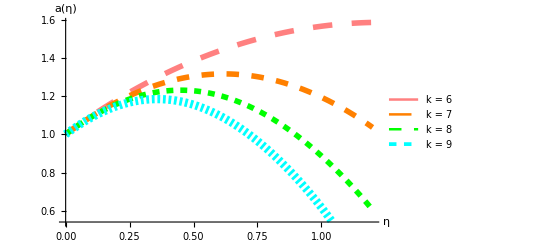

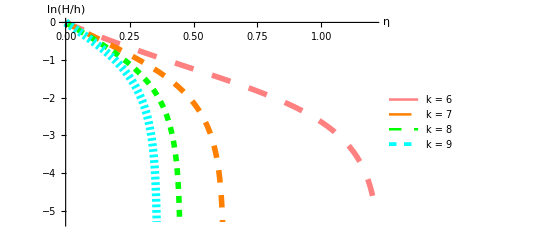

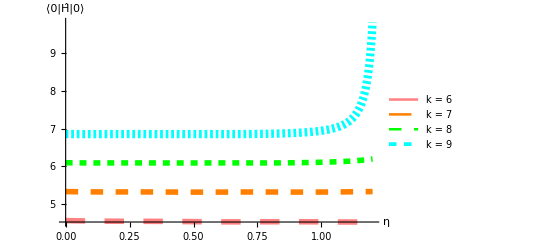

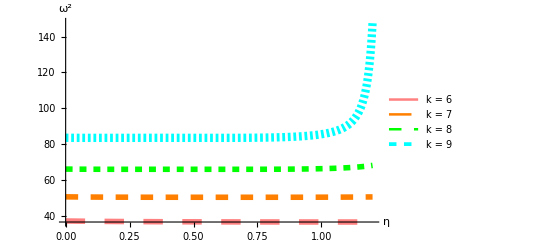

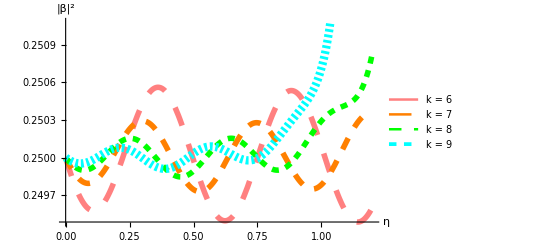

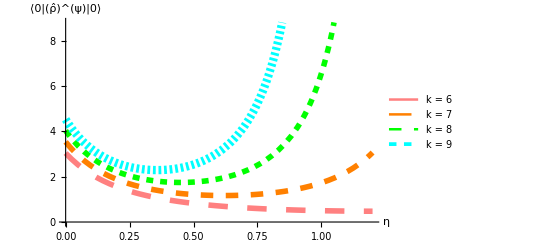

```mathematica
vs1=cqcint[1,1,6,0,3.0`100];
vs2=cqcint[1,1,7,0,1.8`100];
vs3=cqcint[1,1,8,0,1.4`100];
vs4=cqcint[1,1,9,0,1.2`100];
(*cutoff is 5.78*)

Plot[{a[t]/.vs1[[4]],a[t]/.vs2[[4]],a[t]/.vs3[[4]],a[t]/.vs4[[4]](*,a[t]/.ads/.param*)},{t,0,1.2},PlotRange->Automatic,AxesLabel->{"η","a(η)"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"k = 6","k = 7","k = 8","k = 9"(*,"de Sitter"*)},PlotStyle->{{Dashing[Large],Thickness[0.01],Pink},{Dashing[Medium],Thickness[0.01],Orange},{Dashing[Small],Thickness[0.01],Green},{Dashing[Tiny],Thickness[0.015],Cyan}(*,{Thickness[0.005],White}*)}]

Plot[{Log[a'[t]/a[t]^2]/.vs1[[4]],Log[a'[t]/a[t]^2]/.vs2[[4]],Log[a'[t]/a[t]^2]/.vs3[[4]],Log[a'[t]/a[t]^2]/.vs4[[4]](*,Log[a'[t]/a[t]^2]/.ads/.param*)},{t,0,1.2},PlotRange->Automatic,AxesLabel->{"η","ln(H/h)"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"k = 6","k = 7","k = 8","k = 9"},PlotStyle->{{Dashing[Large],Thickness[0.01],Pink},{Dashing[Medium],Thickness[0.01],Orange},{Dashing[Small],Thickness[0.01],Green},{Dashing[Tiny],Thickness[0.015],Cyan}(*,{Thickness[0.005],White}*)}]

Plot[{vs1[[5]],vs2[[5]],vs3[[5]],vs4[[5]]},{t,0,1.2},PlotRange->Automatic,AxesLabel->{"η","⟨0|Ĥ|0⟩"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"k = 6","k = 7","k = 8","k = 9"},PlotStyle->{{Dashing[Large],Thickness[0.01],Pink},{Dashing[Medium],Thickness[0.01],Orange},{Dashing[Small],Thickness[0.01],Green},{Dashing[Tiny],Thickness[0.015],Cyan}}]

Plot[{vs1[[6]],vs2[[6]],vs3[[6]],vs4[[6]]},{t,0,1.2},PlotRange->Automatic,AxesLabel->{"η","ω^2"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"k = 6","k = 7","k = 8","k = 9"},PlotStyle->{{Dashing[Large],Thickness[0.01],Pink},{Dashing[Medium],Thickness[0.01],Orange},{Dashing[Small],Thickness[0.01],Green},{Dashing[Tiny],Thickness[0.015],Cyan}}]

Plot[{vs1[[7]],vs2[[7]],vs3[[7]],vs4[[7]]},{t,0,1.2},PlotRange->Automatic,AxesLabel->{"η","|β|^2"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"k = 6","k = 7","k = 8","k = 9"},PlotStyle->{{Dashing[Large],Thickness[0.01],Pink},{Dashing[Medium],Thickness[0.01],Orange},{Dashing[Small],Thickness[0.01],Green},{Dashing[Tiny],Thickness[0.015],Cyan}}]

Plot[{vs1[[8]],vs2[[8]],vs3[[8]],vs4[[8]]},{t,0,1.2},PlotRange->Automatic,AxesLabel->{"η","⟨0|(ρ̂)^(ψ)|0⟩"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"k = 6","k = 7","k = 8","k = 9"},PlotStyle->{{Dashing[Large],Thickness[0.01],Pink},{Dashing[Medium],Thickness[0.01],Orange},{Dashing[Small],Thickness[0.01],Green},{Dashing[Tiny],Thickness[0.015],Cyan}}]
```

### III. Semiclassical regime

#### Zeroth-order

It is instructive to consider the results without backreaction (i.e., semiclassical result). To do this, we simply neglect the backreaction terms in the previous equations (e.g., ρ_ϕ in the Friedmann equations) and regard the spacetime as exactly described by ads.

The CHO modes satisfy...

```mathematica
ωcho=Solve[ω^2==k^2-1/2(a'[t]^2/a[t]^2+3 H^2 a[t]^2/.ads/.t->ti),ω][[1]];
cho={ξ''[t]+(k^2-a''[t]/a[t]/.ads)ξ[t]==0,χ''[t]+(k^2-a''[t]/a[t]/.ads)χ[t]==0,ξ[ti]==0,ξ'[ti]==√(ω/2),χ[ti]==-1/(√(2ω)),χ'[ti]==0};
```

For the same parameters, we setup the numerical solution...

```mathematica
(*semiclassical result*)
scrint[A0_,H0_,k0_,ti0_,tf0_]:=(
param={ti->ti0,tf->tf0,A->A0,H->H0,k->k0};
solcho=NDSolve[cho/.ωcho/.param,{ξ,χ},{t,ti,tf-10^-3}/.param,WorkingPrecision->30][[1]];
Hvac[t_]=ξ'[t]^2/2+(k^2-a''[t]/a[t])ξ[t]^2+χ'[t]^2/2+(k^2-a''[t]/a[t])χ[t]^2/.ads/.param/.solcho;
ωsq[t_]=k^2-a''[t]/a[t]/.ads/.param;
βsq[t_]=Hvac[t]/(√ωsq[t])-1/2;
{solcho,Hvac[t],ωsq[t],βsq[t],ρϕ[t]/.ρϕvac/.ads/.ωcho/.param/.solcho}
);
(*
Outputs: 1 = (a,ξ,χ), 2 = <0|H|0>(t), 3 = ω^2(t), 4 = |β|^2, 5 = <0|Subscript[ρ, ϕ](t)|0>
*)
```

Comparing the CQC and semiclassical results...

```mathematica
testk2=cqcint[1,1,2,0,1];
testk4=cqcint[1,1,4,0,1];
testk6=cqcint[1,1,6,0,1];
testk8=cqcint[1,1,8,0,1];

semik2=scrint[1,1,2,0,1];
semik4=scrint[1,1,4,0,1];
semik6=scrint[1,1,6,0,1];
semik8=scrint[1,1,8,0,1];
```

And plots of the Hamiltonian...

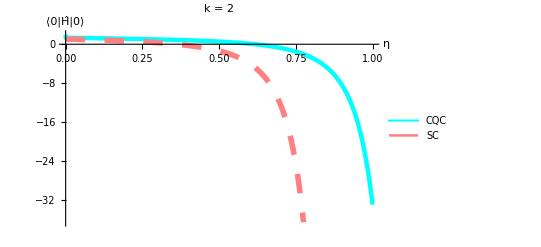

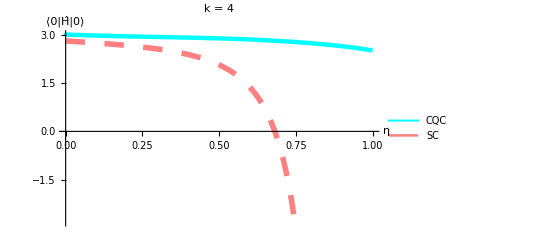

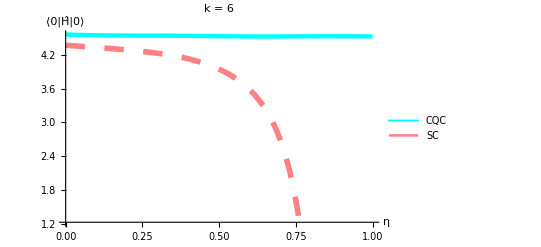

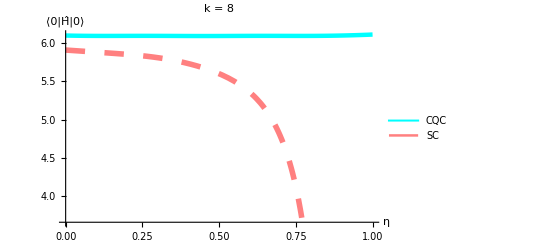

```mathematica
Plot[{testk2[[5]],semik2[[2]]},{t,ti,tf}/.param,PlotRange->Automatic,AxesLabel->{"η","⟨0|Ĥ|0⟩"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red,12],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"CQC","SC"},PlotStyle->{{Thickness[0.008],Cyan},{Dashing[Large],Thickness[0.01],Pink}},PlotLabel->"k = 2"]

Plot[{testk4[[5]],semik4[[2]]},{t,ti,tf}/.param,PlotRange->Automatic,AxesLabel->{"η","⟨0|Ĥ|0⟩"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red,12],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"CQC","SC"},PlotStyle->{{Thickness[0.008],Cyan},{Dashing[Large],Thickness[0.01],Pink}},PlotLabel->"k = 4"]

Plot[{testk6[[5]],semik6[[2]]},{t,ti,tf}/.param,PlotRange->Automatic,AxesLabel->{"η","⟨0|Ĥ|0⟩"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red,12],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"CQC","SC"},PlotStyle->{{Thickness[0.008],Cyan},{Dashing[Large],Thickness[0.01],Pink}},PlotLabel->"k = 6"]

Plot[{testk8[[5]],semik8[[2]]},{t,ti,tf}/.param,PlotRange->Automatic,AxesLabel->{"η","⟨0|Ĥ|0⟩"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red,12],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"CQC","SC"},PlotStyle->{{Thickness[0.008],Cyan},{Dashing[Large],Thickness[0.01],Pink}},PlotLabel->"k = 8"]
```

And plots of the energy density...

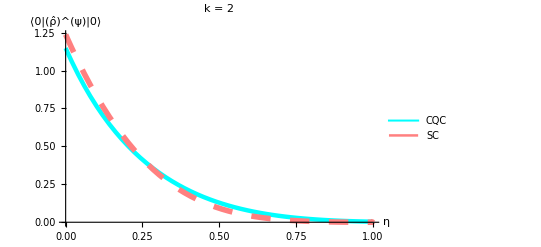

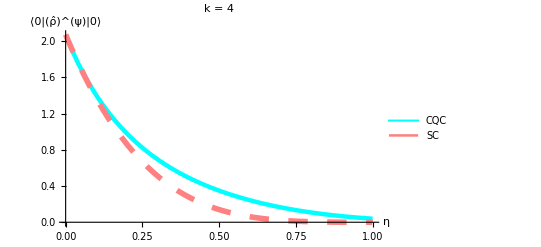

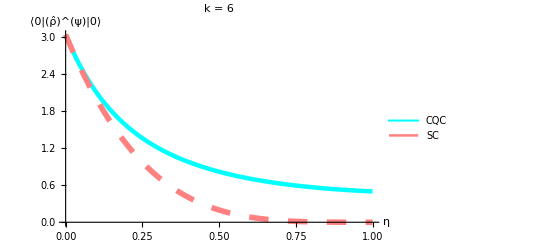

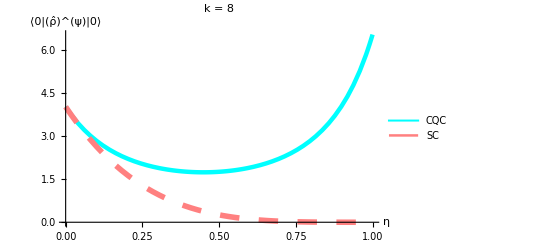

```mathematica
Plot[{testk2[[8]],semik2[[5]]},{t,ti,tf}/.param,PlotRange->Automatic,AxesLabel->{"η","⟨0|(ρ̂)^(ψ)|0⟩"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red,12],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"CQC","SC"},PlotStyle->{{Thickness[0.008],Cyan},{Dashing[Large],Thickness[0.01],Pink}},PlotLabel->"k = 2"]

Plot[{testk4[[8]],semik4[[5]]},{t,ti,tf}/.param,PlotRange->Automatic,AxesLabel->{"η","⟨0|(ρ̂)^(ψ)|0⟩"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red,12],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"CQC","SC"},PlotStyle->{{Thickness[0.008],Cyan},{Dashing[Large],Thickness[0.01],Pink}},PlotLabel->"k = 4"]

Plot[{testk6[[8]],semik6[[5]]},{t,ti,tf}/.param,PlotRange->Automatic,AxesLabel->{"η","⟨0|(ρ̂)^(ψ)|0⟩"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red,12],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"CQC","SC"},PlotStyle->{{Thickness[0.008],Cyan},{Dashing[Large],Thickness[0.01],Pink}},PlotLabel->"k = 6"]

Plot[{testk8[[8]],semik8[[5]]},{t,ti,tf}/.param,PlotRange->Automatic,AxesLabel->{"η","⟨0|(ρ̂)^(ψ)|0⟩"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red,12],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->{"CQC","SC"},PlotStyle->{{Thickness[0.008],Cyan},{Dashing[Large],Thickness[0.01],Pink}},PlotLabel->"k = 8"]
```

#### Leading and next-to-leading corrections

In this section, we construct an algorithm that solves the Einstein-Klein-Gordon system through the perturbative-iterative approach. This begins of course by providing the classical de Sitter solution (zeroth-order) exactly as in done previous section...

```mathematica
ωcho=Solve[ω^2==k^2-1/2(a'[t]^2/a[t]^2+3 H^2 a[t]^2/.ads/.t->ti),ω][[1]];
cho={ξ''[t]+(k^2-a''[t]/a[t]/.ads)ξ[t]==0,χ''[t]+(k^2-a''[t]/a[t]/.ads)χ[t]==0,ξ[ti]==0,ξ'[ti]==√(ω/2),χ[ti]==-1/(√(2ω)),χ'[ti]==0};
scrint[A0_,H0_,k0_,ti0_,tf0_]:=(
param={ti->ti0,tf->tf0,A->A0,H->H0,k->k0};
solcho=NDSolve[cho/.ωcho/.param,{ξ,χ},{t,ti,tf-10^-3}/.param,WorkingPrecision->30][[1]];
Hvac[t_]=ξ'[t]^2/2+(k^2-a''[t]/a[t])ξ[t]^2+χ'[t]^2/2+(k^2-a''[t]/a[t])χ[t]^2/.ads/.param/.solcho;
ωsq[t_]=k^2-a''[t]/a[t]/.ads/.param;
βsq[t_]=Hvac[t]/(√ωsq[t])-1/2;
{solcho,Hvac[t],ωsq[t],βsq[t],ρϕ[t]/.ρϕvac/.ads/.ωcho/.param/.solcho,param}
);
```

Provided then a solution ρ_ϕ(t) obtained for example through scrint[...], we setup a function that solves for the corresponding scale factor (with the same parameters)...

```mathematica
SolveScaleFactor[ρϕsol_]:=(
param=ρϕsol[[6]];
ρϕinit0=ρϕsol[[5]]/.t->0;
ρϕi=ρϕsol[[5]];
FriedmannConstraint=fe1/.t->ti/.ainit/.ρϕ[ti]->ρϕinit0/.param;
HubbleEquation=fe12/.PΛ->-ρΛ/.Solve[FriedmannConstraint,ρΛ][[1]];
NSol=NDSolve[{HubbleEquation/.ρϕ[t]->ρϕi,a[0]==(a[ti]/.ainit[[1]]/.param),a'[0]==(a'[ti]/.ainit[[2]]/.param)},a,{t,0,(tf/.param)-10^-3}][[1]];
{NSol,param}
);
```

To check whether this program works, we compare the results of the CQC vs the LO result for k=8...

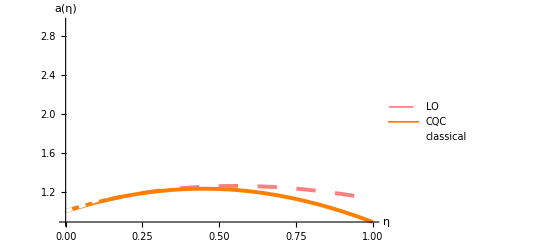

```mathematica
cqcaϕ=cqcint[1,1,8,0,1];

(*leading order backreaction*)
o1ϕ=scrint[1,1,8,0,1];
o1a=SolveScaleFactor[o1ϕ];

Plot[{a[t]/.o1a[[1]],a[t]/.cqcaϕ[[4]],a[t]/.ads/.{A->1,H->1}},{t,0,1-10^-3},PlotRange->Automatic,AxesLabel->{"η","a(η)"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red,12],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->Placed[{"LO","CQC","classical"},Below],PlotStyle->{{Dashing[Large],Thickness[0.007],Pink},{Thickness[0.007],Orange},{Dashing[Small],Thickness[0.007],White}}]
```

It can be seen that leading-order calculation appears to approach the CQC. This improves further in higher order iterations. 

It should also be mentioned that the first-order calculation is remarkably more accurate for longer wavelengths. However, for k<1.5 the LO result returns a complex a(t) and therefore cannot be trusted in this regime. This appears to be rooted from the fact that in the LO frequency (for A=1 and H=1) is given by...

```mathematica
"ω"==(ω/.ωcho/.ti->0/.A->1/.H->1)
```

ω==√(-2+k^2)

This becomes purely imaginary below k=√2 and in fact this can be confirmed to be the lower bound to k before the LO result becomes complex. We shall get back to this later.

Continuing to the next-to-leading-order (NLO), we build a function that computes ρ_ϕ provided the scale factor. This is already much like scrint[...] and so we just build on this...

```mathematica
SolveScalarField[asol_]:=(
param=asol[[2]];
ω[t_]=√(k^2-a''[t]/a[t])/.asol[[1]]/.param;
ω0=ω[0];
ϕsystem={ξ''[t]+ω[t]^2 ξ[t]==0,χ''[t]+ω[t]^2 χ[t]==0,ξ[0]==0,ξ'[0]==√(ω0/2),χ[0]==-1/(√(2ω0)),χ'[0]==0};
Nϕsol=NDSolve[ϕsystem,{ξ,χ},{t,0,(tf/.param)-10^-3}][[1]];
Hvac[t_]=ξ'[t]^2/2+(k^2-a''[t]/a[t])ξ[t]^2+χ'[t]^2/2+(k^2-a''[t]/a[t])χ[t]^2/.asol[[1]]/.param/.Nϕsol;
ωsq[t_]=ω[t]^2;
βsq[t_]=Hvac[t]/ω[t]-1/2;
{solcho,Hvac[t],ωsq[t],βsq[t],ρϕ[t]/.ρϕvac/.param/.Nϕsol/.asol[[1]],param}
);
```

Testing this using the previous iteration o1a, we obtain...

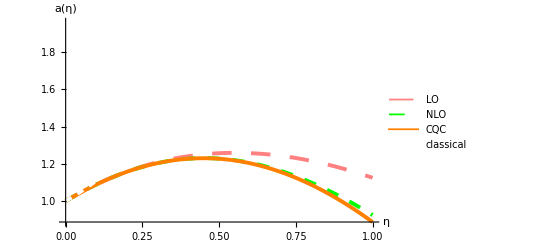

```mathematica
o2ϕ=SolveScalarField[o1a];
o2a=SolveScaleFactor[o2ϕ];

Plot[{a[t]/.o1a[[1]],a[t]/.o2a[[1]],a[t]/.cqcaϕ[[4]],a[t]/.ads/.{A->1,H->1}},{t,0,1-10^-3},PlotRange->Automatic,AxesLabel->{"η","a(η)"},AxesStyle->Directive[Red,15],LabelStyle->Directive[Red,12],Ticks->Automatic,TicksStyle->Directive[Red,15],PlotLegends->Placed[{"LO","NLO","CQC","classical"},Below],PlotStyle->{{Dashing[Large],Thickness[0.007],Pink},{Dashing[Medium],Thickness[0.007],Green},{Thickness[0.007],Orange},{Dashing[Small],Thickness[0.007],White}}]
```

This supports the conclusion that the iterative method approaches the CQC for higher orders. But above all it shows that the CQC is superior to the iterative method.